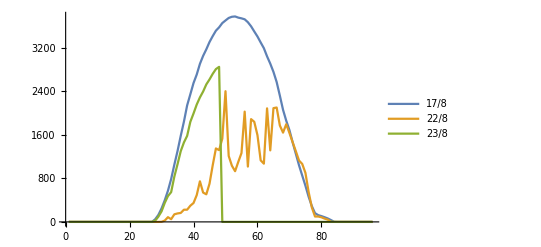

```mathematica
(* change name of imported csv, change dates in ListLinePlot to dates exisiting in data *)

data = Import["C:\\Users\\s156757\\OneDrive\\SolArduino\\solarduino\\Documentation\\Mathematica\\data17_23.csv"];
data = Delete[data,1];

f[d_] := ( (* params: date, returns list of values for that date *)
dayData = Select[data,
DayCount[
DateObject[DateObject[
DateString[#[[1]],{"Day","-","Month","-","Year"," ","Hour",":","Minute"}]
],{0,0}] (* change hour to 0 to compare *) ,
d
] == 0 &
];
Table[dayData[[i]][[2]] ,{i,1,Length[dayData]}]
)

(*ListLinePlot[
f[DateObject[{2016,5,13,0,0}]]
]*)
(*
ListLinePlot[
{
f[DateObject[{2016,8,16,0,0}]],
f[DateObject[{2016,8,17,0,0}]],
f[DateObject[{2016,8,18,0,0}]],
f[DateObject[{2016,8,19,0,0}]]
},PlotLegends -> {"24","24","40","5"}
]*)

ListLinePlot[
{
f[DateObject[{2016,8,17,0,0}]],
f[DateObject[{2016,8,22,0,0}]],
f[DateObject[{2016,8,23,0,0}]],
},
PlotLegends -> {"17/8","22/8","23/8"}
]




(*Select[data,DateDifference[DateObject[ #[[1]]],{2016,8,18,0,0} ]≤ 0 &,1 ]*)
```

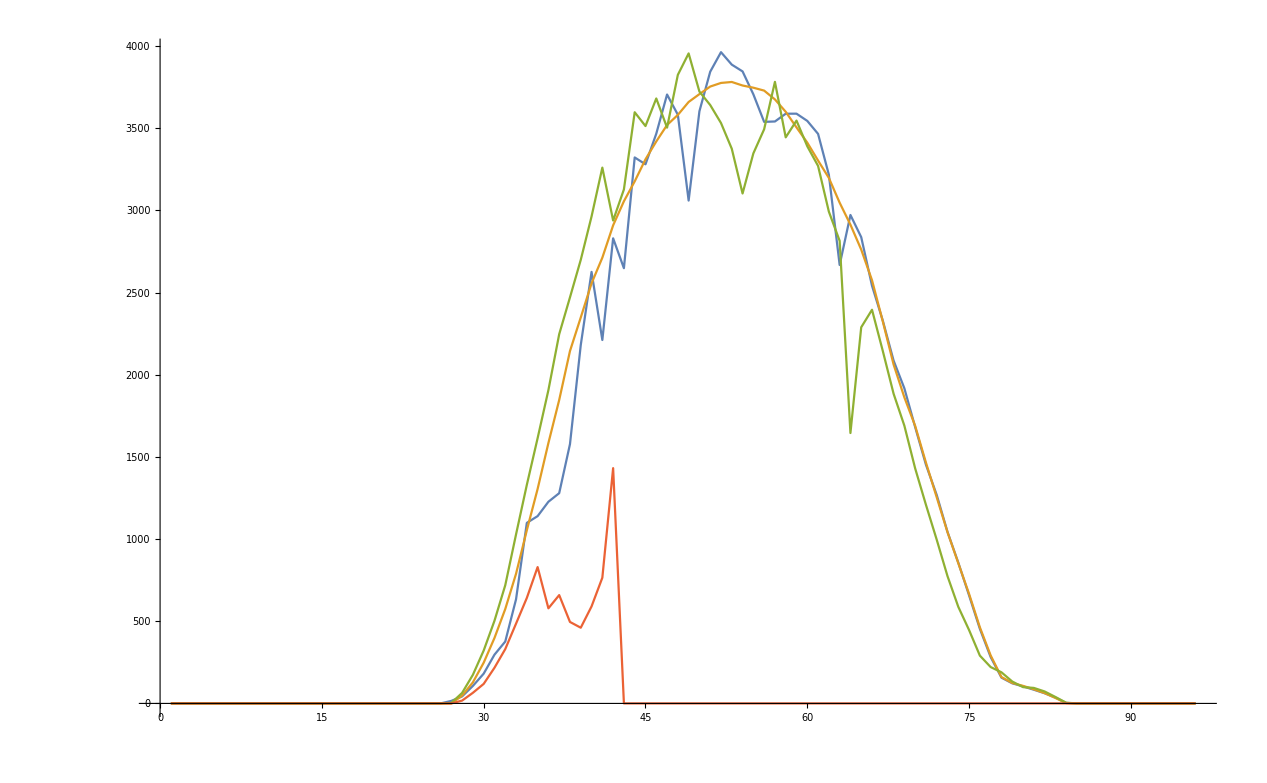

```mathematica
data 17/8 {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47.5,128.167,247.833,398.167,574.333,789,1053.83,1304.83,1584.33,1846.17,2144,2348.33,2555.83,2712,2908.67,3055.33,3176.33,3310.33,3419.17,3519.17,3580.67,3659.33,3707.17,3753.17,3775.17,3781,3759.5,3746.17,3728.5,3675,3599.67,3504.67,3411.83,3302.83,3197.33,3046.5,2912.83,2761.17,2574.83,2324.33,2062.5,1862.17,1688.83,1465,1254,1041.5,853.167,666,463,291.833,160.667,124.333,106.833,86,62.8333,33.3333,2,0,0,0,0,0,0,0,0,0,0,0,0}

full data {{"17-08-2016 0:00",0},{"17-08-2016 0:15",0},{"17-08-2016 0:30",0},{"17-08-2016 0:45",0},{"17-08-2016 1:00",0},{"17-08-2016 1:15",0},{"17-08-2016 1:30",0},{"17-08-2016 1:45",0},{"17-08-2016 2:00",0},{"17-08-2016 2:15",0},{"17-08-2016 2:30",0},{"17-08-2016 2:45",0},{"17-08-2016 3:00",0},{"17-08-2016 3:15",0},{"17-08-2016 3:30",0},{"17-08-2016 3:45",0},{"17-08-2016 4:00",0},{"17-08-2016 4:15",0},{"17-08-2016 4:30",0},{"17-08-2016 4:45",0},{"17-08-2016 5:00",0},{"17-08-2016 5:15",0},{"17-08-2016 5:30",0},{"17-08-2016 5:45",0},{"17-08-2016 6:00",0},{"17-08-2016 6:15",0},{"17-08-2016 6:30",0},{"17-08-2016 6:45",47.5},{"17-08-2016 7:00",128.167},{"17-08-2016 7:15",247.833},{"17-08-2016 7:30",398.167},{"17-08-2016 7:45",574.333},{"17-08-2016 8:00",789},{"17-08-2016 8:15",1053.83},{"17-08-2016 8:30",1304.83},{"17-08-2016 8:45",1584.33},{"17-08-2016 9:00",1846.17},{"17-08-2016 9:15",2144},{"17-08-2016 9:30",2348.33},{"17-08-2016 9:45",2555.83},{"17-08-2016 10:00",2712},{"17-08-2016 10:15",2908.67},{"17-08-2016 10:30",3055.33},{"17-08-2016 10:45",3176.33},{"17-08-2016 11:00",3310.33},{"17-08-2016 11:15",3419.17},{"17-08-2016 11:30",3519.17},{"17-08-2016 11:45",3580.67},{"17-08-2016 12:00",3659.33},{"17-08-2016 12:15",3707.17},{"17-08-2016 12:30",3753.17},{"17-08-2016 12:45",3775.17},{"17-08-2016 13:00",3781},{"17-08-2016 13:15",3759.5},{"17-08-2016 13:30",3746.17},{"17-08-2016 13:45",3728.5},{"17-08-2016 14:00",3675},{"17-08-2016 14:15",3599.67},{"17-08-2016 14:30",3504.67},{"17-08-2016 14:45",3411.83},{"17-08-2016 15:00",3302.83},{"17-08-2016 15:15",3197.33},{"17-08-2016 15:30",3046.5},{"17-08-2016 15:45",2912.83},{"17-08-2016 16:00",2761.17},{"17-08-2016 16:15",2574.83},{"17-08-2016 16:30",2324.33},{"17-08-2016 16:45",2062.5},{"17-08-2016 17:00",1862.17},{"17-08-2016 17:15",1688.83},{"17-08-2016 17:30",1465},{"17-08-2016 17:45",1254},{"17-08-2016 18:00",1041.5},{"17-08-2016 18:15",853.167},{"17-08-2016 18:30",666},{"17-08-2016 18:45",463},{"17-08-2016 19:00",291.833},{"17-08-2016 19:15",160.667},{"17-08-2016 19:30",124.333},{"17-08-2016 19:45",106.833},{"17-08-2016 20:00",86},{"17-08-2016 20:15",62.8333},{"17-08-2016 20:30",33.3333},{"17-08-2016 20:45",2},{"17-08-2016 21:00",0},{"17-08-2016 21:15",0},{"17-08-2016 21:30",0},{"17-08-2016 21:45",0},{"17-08-2016 22:00",0},{"17-08-2016 22:15",0},{"17-08-2016 22:30",0},{"17-08-2016 22:45",0},{"17-08-2016 23:00",0},{"17-08-2016 23:15",0},{"17-08-2016 23:30",0},{"17-08-2016 23:45",0}}
```

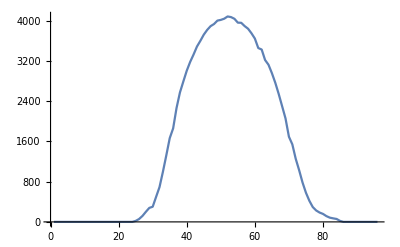
```mathematica
13/5 -Graphics-
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19.5,57,118.667,200.833,278,301.333,497.667,691.5,995.667,1323.5,1663,1857.33,2262.67,2571,2789.83,3003,3177.5,3324.5,3483.17,3597,3719.33,3813.67,3888,3929.83,3997.83,4012.33,4036,4080.5,4067.67,4034,3957.67,3954.33,3889.17,3837,3746.83,3641.67,3453.33,3423.67,3215.5,3121.83,2954.5,2762.67,2541,2298.83,2055.33,1692,1540.17,1253,1027.17,782,579,419.5,295,226.833,185.833,158.667,115,84.5,70.1667,58.1667,20.1667,0,0,0,0,0,0,0,0,0,0,0}
```